```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\zhangchenhui\custcal

## 函数定义

```mathematica
核算设计=<|"核算设计文本"->Import["custcal.org","Text",CharacterEncoding->"UTF8"]|>;

AssociateTo[核算设计,(* 各表格项内容 *)
RightComposition[
StringCases[
StringExpression[
StartOfLine~~"#+NAME: ",
type:(WordCharacter..)~~":",
(tname:LetterCharacter..)~~Whitespace,
tcnt:Shortest["|-"~~__~~"-|\n"],
"\n"]:>
(tname->
With[{tb=Map[StringTrim@*ToString,
ImportString[
StringReplace[tcnt,{StartOfLine~~"|"~~("+"|"-"|"|"|" ")..~~"|\n"->""}],
"Table","FieldSeparators"->{"|"},"LineSeparators"->{"|\n"}],{2}]},
Switch[type,
"tab",AssociationThread[tb[[2;;,1]]->Map[AssociationThread[Rest@First@tb->#]&,tb[[2;;,2;;]]]],
_,Map[AssociationThread[First[tb]->#]&,Rest[tb]]]])],
Merge[Apply@Join]
]@核算设计["核算设计文本"]];

AppendTo[核算设计,(* 存储过程名称，来自数据库查询 *)
"存储过程名称"->
<|"110434"->"sp_Cust_QT_Gqzq","140001"->"sp_Cust_CASH_Xjc","140002"->"sp_Cust_CASH_Czc","140004"->"sp_Cust_CASH_Zpc","140008"->"sp_Cust_CASH_Xjlb","140009"->"sp_Cust_CASH_Zplb","140011"->"sp_Cust_CASH_Lxgb","140021"->"sp_Cust_CASH_Xjq","140022"->"sp_Cust_CASH_Czq","140024"->"sp_Cust_CASH_Zpq","140029"->"sp_Cust_CASH_Xjhc","140030"->"sp_Cust_CASH_Zphc","140055"->"sp_Cust_CASH_Hzc","140057"->"sp_Cust_CASH_Hzq","140203"->"sp_Cust_HLHG_Cyks","140205"->"sp_Cust_HLHG_Kslb","140211"->"sp_Cust_CASH_Otcr","140212"->"sp_Cust_CASH_Otcc","150001"->"sp_Cust_ZTG_Zqhc","150002"->"sp_Cust_ZTG_Zqlb","150032"->"sp_Cust_HLHG_Hlrl","160021"->"sp_Cust_SFCG_Yhzq","160022"->"sp_Cust_SFCG_Zqyh","160031"->"sp_Cust_SFCG_Tzc","160032"->"sp_Cust_SFCG_Tzq","168007"->"sp_Cust_SFCG_Tzzr","168008"->"sp_Cust_SFCG_Tzzc","220000"->"sp_Cust_PT_Buy","220006"->"sp_Cust_BJHG_Rqhg","220007"->"sp_Cust_YDGH_Ydhg","220010"->"sp_Cust_HLHG_Hgrz","220012"->"sp_Cust_PG_Pgjk","220030"->"sp_Cust_PG_Psgf","220031"->"sp_Cust_PG_Psjk","220032"->"sp_Cust_QT_Zdjy","220033"->"sp_Cust_QT_Cxzd","220035"->"sp_Cust_BJHG_Rzgh","220038"->"sp_Cust_ETF_Jjsg","220041"->"sp_Cust_ETF_Tdkk","220043"->"sp_Cust_YDGH_Rzgh","220049"->"sp_Cust_KFJJ_JJsg","220058"->"sp_Cust_ZZXQ_Xqkk","220059"->"sp_Cust_ZZXQ_Xqzg","220090"->"sp_Cust_KFJJ_Zhsg","220091"->"sp_Cust_KFJJ_Zhsh","220094"->"sp_Cust_HGT_Buy","220095"->"sp_Cust_HGT_Sale","220096"->"sp_Cust_HGT_Hlff","220097"->"sp_Cust_HGT_Zhf","220099"->"sp_Cust_HGT_Qzmc","220100"->"sp_Cust_PT_Tnmr","220118"->"sp_Cust_HGT_Zdjy","220119"->"sp_Cust_HGT_Czjy","220121"->"sp_Cust_HGT_Gong","221001"->"sp_Cust_PT_Sale","221003"->"sp_Cust_BJHG_Rzhg","221004"->"sp_Cust_YDGH_Rzhg","221007"->"sp_Cust_HLHG_Hlrz","221008"->"sp_Cust_ZQ_Zqdx","221009"->"sp_Cust_ZQ_Zqdf","221011"->"sp_Cust_PG_Pgqz","221013"->"sp_Cust_PG_Pgrz","221023"->"sp_Cust_BJHG_Rztq","221033"->"sp_Cust_BJHG_Rqgh","221034"->"sp_Cust_BJHG_Rqtq","221036"->"sp_Cust_ETF_Sgjg","221042"->"sp_Cust_QT_Xsks","221043"->"sp_Cust_YDGH_Rqgh","221049"->"sp_Cust_KFJJ_Jjsh","221101"->"sp_Cust_PT_Tnmc","222003"->"sp_Cust_ZTG_Ztgf","222004"->"sp_Cust_QT_Tpqr","222006"->"sp_Cust_QT_Cxsf","240507"->"sp_Cust_KFJJ_Hlbr","550001"->"sp_Cust_RZRQ_Dbmr","550002"->"sp_Cust_RZRQ_Rzmr","550003"->"sp_Cust_RZRQ_Mqhk","552003"->"sp_Cust_RZRQ_Rqfy","553001"->"sp_Cust_RZRQ_Rzjr","553002"->"sp_Cust_RZRQ_Rzjc","940008"->"sp_Cust_SFCG_Xjlb","940029"->"sp_Cust_SFCG_Xjhc","140032"->"sp_Cust_CASH_Fxgb","140124"->"sp_Cust_CASH_Czpq","140200"->"sp_Cust_GPZY_Lxks","140202"->"sp_Cust_CASH_Zpqr","140502"->"sp_Cust_BRBC_Bxhc","150028"->"sp_Cust_ZTG_Nbzc","150030"->"sp_Cust_HLHG_Gfrl","150031"->"sp_Cust_ZTG_Ncqx","160024"->"sp_Cust_SFCG_Czzy","220003"->"sp_Cust_ZYHG_Rqhg","220004"->"sp_Cust_XG_Xgrz","220005"->"sp_Cust_ZTG_Gfzr","220015"->"sp_Cust_ZTG_Ztgr","220016"->"sp_Cust_QT_Zdrz","220023"->"sp_Cust_XG_Xgsg","220024"->"sp_Cust_LOF_Reng","220027"->"sp_Cust_XG_Sgzq","220034"->"sp_Cust_ZYHG_Rzgh","220039"->"sp_Cust_ETF_Shzg","220040"->"sp_Cust_ETF_Sgbk","220042"->"sp_Cust_ETF_Cekk","220047"->"sp_Cust_ETF_Sgsf","220048"->"sp_Cust_ETF_Shsf","220056"->"sp_Cust_KFJJ_Cfzg","220057"->"sp_Cust_KFJJ_Hbzg","220060"->"sp_Cust_ZYHG_Zyck","220084"->"sp_Cust_LOF_Szsg","220085"->"sp_Cust_LOF_Szsh","220114"->"sp_Cust_HGT_Sgss","220116"->"sp_Cust_HGT_Fjyc","220135"->"sp_Cust_LOF_Qrkk","220136"->"sp_Cust_LOF_Qrfk","220137"->"sp_Cust_KFJJ_Jjsz","220138"->"sp_Cust_KFJJ_Jjxz","221002"->"sp_Cust_ZYHG_Rzhg","221006"->"sp_Cust_ZTG_Gfzc","221012"->"sp_Cust_PG_Tktx","221014"->"sp_Cust_ZTG_Ztgc","221017"->"sp_Cust_ZZZG_Hszc","221019"->"sp_Cust_ZZZG_Shzj","221024"->"sp_Cust_XG_Sghk","221032"->"sp_Cust_QT_Czzc","221035"->"sp_Cust_ZYHG_Rqgh","221037"->"sp_Cust_ETF_Jjsh","221038"->"sp_Cust_ETF_Sgtk","221039"->"sp_Cust_ETF_Cefk","221040"->"sp_Cust_ETF_Xjtd","221056"->"sp_Cust_KFJJ_Hbjg","221057"->"sp_Cust_KFJJ_Cfjg","221060"->"sp_Cust_ZYHG_Zyrk","221204"->"sp_Cust_GPZY_Csrz","221207"->"sp_Cust_GPZY_Csrq","221243"->"sp_Cust_GPZY_Rzgh","221251"->"sp_Cust_GPZY_Jfbz","221253"->"sp_Cust_GPZY_Jfbf","221343"->"sp_Cust_GPZY_Rqgh","221350"->"sp_Cust_GZYF_Edzc","221351"->"sp_Cust_GZYF_Edzx","240508"->"sp_Cust_KFJJ_Rgbc","240509"->"sp_Cust_KFJJ_Sgbc","240510"->"sp_Cust_KFJJ_Dsde","240511"->"sp_Cust_KFJJ_Shbr","240512"->"sp_Cust_KFJJ_Qsbr","240513"->"sp_Cust_KFJJ_Rgsb","240514"->"sp_Cust_KFJJ_Sgsb","240515"->"sp_Cust_KFJJ_Dssb","240562"->"sp_Cust_BRBC_Ksbr","260508"->"sp_Cust_BRBC_Jrbc","260512"->"sp_Cust_BRBC_Jrqs","550004"->"sp_Cust_RZRQ_Rzpc","550005"->"sp_Cust_RZRQ_Dbmc","550007"->"sp_Cust_RZRQ_Mqhq","551001"->"sp_Cust_RZRQ_Dbzr","551004"->"sp_Cust_RZRQ_Rqzr","551005"->"sp_Cust_RZRQ_Dbzc","551007"->"sp_Cust_RZRQ_Hqhc","551008"->"sp_Cust_RZRQ_Yqzc","551020"->"sp_Cust_RZRQ_Fcjj","551021"->"sp_Cust_RZRQ_Fcjz","552001"->"sp_Cust_RZRQ_Rzlx","552006"->"sp_Cust_RZRQ_Yqlx","552008"->"sp_Cust_RZRQ_Qyje","552009"->"sp_Cust_RZRQ_Yqfy","552011"->"sp_Cust_RZRQ_Ylfx","552012"->"sp_Cust_RZRQ_Yzfx","552015"->"sp_Cust_RZRQ_Yffx","552017"->"sp_Cust_RZRQ_Fzbj","552018"->"sp_Cust_RZRQ_Rqfz","552034"->"sp_Cust_RZRQ_Tcqe","552036"->"sp_Cust_RZRQ_Tckx","554007"->"sp_Cust_RZRQ_Qzye","580509"->"sp_Cust_ZZXQ_Tjsd"|>];
```

## 存储过程

### 存储过程管理

```mathematica
Needs["DatabaseLink`"]
conn=OpenSQLConnection[JDBC["Microsoft SQL Server(jTDS)", 
  "10.237.1.10:1433/CustCal"], "Username" -> "sa", "Password" -> "qyb20qyb20","ReadOnly"->True]
```

#### 数据库查询存储过程名称

```mathematica
Association[(ToString[First[#]]->Last[#])&/@SQLSelect[conn,"digest_ext",{"digestid","spname"}]]
```

#### 数据库删除所有sp_Cust存储过程

```mathematica
Scan[SQLExecute[conn,#]&,
"drop proc "<>#&/@ Flatten@SQLExecute[conn,"select name from sysobjects where type='P' and name like 'sp_Cust%'"]]
```

#### 数据库更新sp_Cust存储过程

```mathematica
Scan[SQLExecute[conn,#]&,
Query[Flatten,StringSplit[Import[#,"Text",CharacterEncoding->"Unicode"],{"go","GO"}]&]@FileNames["sp/*.sql"]]
```

```mathematica
CloseSQLConnection[conn]
```

{}

### 本地生成存储过程

```mathematica
Query[
"核算办法",
Select[#产生方式=="模板"∧#进度=="完成"&],
Export[FileNameJoin[{"sp",核算设计["存储过程名称"][#业务摘要]<>".sql"}],
TemplateApply[
Import[FileNameJoin[{"templates",#核算类型<>".template"}],"Text",CharacterEncoding->"UTF8"],
Join[
Query["核算对象",All,"数据库对象"]@核算设计,
#,
<|"存储过程"->核算设计["存储过程名称"][#业务摘要],"流通类型"->If[StringLength[#流通类型]==1,"0"<>#流通类型,#流通类型]|>
]],"Text",CharacterEncoding->"Unicode"]&]@核算设计//Column
```

sp\sp_Cust_PT_Buy.sql
sp\sp_Cust_PT_Tnmr.sql
sp\sp_Cust_HGT_Buy.sql
sp\sp_Cust_HGT_Gong.sql
sp\sp_Cust_YDGH_Rzgh.sql
sp\sp_Cust_YDGH_Ydhg.sql
sp\sp_Cust_KFJJ_Zhsg.sql
sp\sp_Cust_RZRQ_Dbmr.sql
sp\sp_Cust_PT_Sale.sql
sp\sp_Cust_PT_Tnmc.sql
sp\sp_Cust_HGT_Sale.sql
sp\sp_Cust_HGT_Qzmc.sql
sp\sp_Cust_YDGH_Rzhg.sql
sp\sp_Cust_YDGH_Rqgh.sql
sp\sp_Cust_KFJJ_Zhsh.sql
sp\sp_Cust_BJHG_Rqhg.sql
sp\sp_Cust_BJHG_Rqgh.sql
sp\sp_Cust_BJHG_Rqtq.sql
sp\sp_Cust_PG_Pgqz.sql
sp\sp_Cust_PG_Pgjk.sql
sp\sp_Cust_ZZXQ_Xqkk.sql
sp\sp_Cust_PG_Psjk.sql
sp\sp_Cust_PG_Psgf.sql
sp\sp_Cust_ZZXQ_Xqzg.sql
sp\sp_Cust_PG_Pgrz.sql
sp\sp_Cust_HLHG_Hlrz.sql
sp\sp_Cust_HGT_Hlff.sql
sp\sp_Cust_KFJJ_Hlbr.sql
sp\sp_Cust_HLHG_Hlrl.sql
sp\sp_Cust_HLHG_Hgrz.sql
sp\sp_Cust_ZQ_Zqdx.sql
sp\sp_Cust_ZQ_Zqdf.sql
sp\sp_Cust_QT_Cxsf.sql
sp\sp_Cust_HGT_Zhf.sql
sp\sp_Cust_ZTG_Ztgf.sql
sp\sp_Cust_QT_Xsks.sql
sp\sp_Cust_BJHG_Rztq.sql
sp\sp_Cust_BJHG_Rzhg.sql
sp\sp_Cust_BJHG_Rzgh.sql
sp\sp_Cust_QT_Zdjy.sql
sp\sp_Cust_QT_Cxzd.sql
sp\sp_Cust_HGT_Zdjy.sql
sp\sp_Cust_HGT_Czjy.sql
sp\sp_Cust_QT_Gqzq.sql
sp\sp_Cust_QT_Tpqr.sql
sp\sp_Cust_SFCG_Xjlb.sql
sp\sp_Cust_SFCG_Xjhc.sql
sp\sp_Cust_CASH_Xjlb.sql
sp\sp_Cust_CASH_Xjhc.sql
sp\sp_Cust_CASH_Zplb.sql
sp\sp_Cust_CASH_Zphc.sql
sp\sp_Cust_SFCG_Yhzq.sql
sp\sp_Cust_CASH_Czc.sql
sp\sp_Cust_CASH_Xjc.sql
sp\sp_Cust_SFCG_Tzc.sql
sp\sp_Cust_CASH_Zpc.sql
sp\sp_Cust_CASH_Otcr.sql
sp\sp_Cust_SFCG_Tzzr.sql
sp\sp_Cust_CASH_Hzc.sql
sp\sp_Cust_SFCG_Zqyh.sql
sp\sp_Cust_CASH_Czq.sql
sp\sp_Cust_CASH_Xjq.sql
sp\sp_Cust_CASH_Zpq.sql
sp\sp_Cust_CASH_Otcc.sql
sp\sp_Cust_SFCG_Tzzc.sql
sp\sp_Cust_SFCG_Tzq.sql
sp\sp_Cust_CASH_Hzq.sql

## 草稿

```mathematica
Subsets[Range[4],2]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
SparseArray
```

```mathematica
findNCL[n_]:=With[{lines=Select[Subsets[Range[0,26],{3}],MatrixRank[Differences@IntegerDigits[#,3,3]]==1&]},
SelectFirst[Subsets[Range[0,26],{n}],s↦AllTrue[lines,ln↦!ContainsAll[s,ln]]]]
```

```mathematica
ParallelMap[findNCL,{16,17,18}]
```

{{0,1,3,5,7,8,9,11,15,17,19,20,21,23,24,25},Missing[NotFound],Missing[NotFound]}

```mathematica
NCL=IntegerDigits[First[%],3,3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,2},{0,2,1},{0,2,2},{1,0,0},{1,0,2},{1,2,0},{1,2,2},{2,0,1},{2,0,2},{2,1,0},{2,1,2},{2,2,0},{2,2,1}}

```mathematica
Graphics3D[{Ball[NCL,0.1], Opacity[0.1],Cuboid[{0,0,0},{2,2,2}]},Boxed->False]
```

```mathematica
Binomial[16,2] 11
```

1320

```mathematica
Binomial[16,3]
```

560

```mathematica
Differences@IntegerDigits[{21,24,25},3,3]
```

{{0,1,0},{0,0,1}}

```mathematica
Equal@@Subtract@@IntegerDigits[Differences[{21,24,25}],3,3]
```

False

```mathematica
Divide
```

```mathematica
Unequal@@({1,2,3}/{3,6,8})
```

False

```mathematica
Unequal[2,3,3]
```

False

```mathematica
Table[Binomial[k,i],{i,1,5},{k,1,5}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5
0 | 1 | 3 | 6 | 10
0 | 0 | 1 | 4 | 10
0 | 0 | 0 | 1 | 5
0 | 0 | 0 | 0 | 1)

```mathematica
m[n_]:=ReplacePart[{i_,j_}/;EvenQ[i]&&j==i/2:>-1]@Table[Binomial[k,i],{i,n},{k,n}]
```

```mathematica
m[4]//MatrixRank
```

4

```mathematica
Table[Binomial[k,i],{i,1,5},{k,1,5}].{-2,1,0,0,0}
```

{0,1,0,0,0}

```mathematica
NullSpace[m[5]]
```

{{-2,1,0,0,0}}

```mathematica
m[5].{-2,1,0,0,0}
```

{0,0,0,0,0}

```mathematica
m[6]//MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 2 | 3 | 4 | 5 | 6
0 | 0 | 0 | 3 | 6 | 10 | 15
0 | 0 | 0 | 1 | 4 | 10 | 20
0 | 0 | 0 | 0 | 0 | 5 | 15
0 | 0 | 0 | 0 | 0 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LinearSolve[Table[Binomial[k,i],{i,0,5},{k,0,5}],{a0,0,a2,0,a4,a5}]
```

{a0+a2+a4-a5,-2 a2-4 a4+5 a5,a2+6 a4-10 a5,-2 (2 a4-5 a5),a4-5 a5,a5}

```mathematica
Sum[Binomial[k,i] x^i]
```

```mathematica
CoefficientList[Sum[2 Subscript[a, i] x(1+x)^i,{i,20}],x]//List
```

```mathematica
FindInstance[{111101111m==(10^n-1)/9,m>0,n>0},{m,n},Integers]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[{111101111 m==1/9 (-1+10^n),m>0,n>0},{m,n},Integers]

```mathematica
NestWhile[10#+1&,1,!Divisible[#,111101111]&]//IntegerDigits//Length
```

220

```mathematica
Clear[f]
f[n_]:=
Cases[Permutations[Range[n]],p_/;AllTrue[p[[#]]&/@Flatten[Table[i;;j,{i,n-2},{j,i+2,n}],1],!MemberQ[#,(First[#]+Last[#])/2]&]]
```

```mathematica
(f/*Length)/@Range[9]
```

{1,2,4,10,20,48,104,282,496}

```mathematica
t=RandomInteger[{0,1},10]
```

{1,1,0,1,1,1,1,0,0,0}

```mathematica
t[[{{1;;3},3,2}]]
```

Part::pkspec1: The expression {{1;;3},3,2} cannot be used as a part specification.

{1,1,0,1,1,1,1,0,0,0}⟦{{1;;3},3,2}⟧

```mathematica
∀
```

```mathematica
Extract[{1,1,0,1,1,1,1,0,0,0},{{1;;3}}]
```

Extract::psl1: Position specification {{1;;3}} in Extract[{1,1,0,1,1,1,1,0,0,0},{{1;;3}}] is not applicable.

Extract[{1,1,0,1,1,1,1,0,0,0},{{1;;3}}]

```mathematica
f[n_]:=Count[Tuples[{0,1},n],p_/;AllTrue[p[[#]]&/@Flatten[Table[i;;j,{i,n-2},{j,i+2,n}],1],Abs[2Total[#]-Length[#]]<=2&]]
```

```mathematica
Array[f,14]
```

{2,4,6,10,14,22,30,46,62,94,126,190,254,382}

```mathematica
FindGeneratingFunction[{2,4,6,10,14,22,30,46,62,94,126,190,254,382},x]//Factor
```

-(2 (-1-x+x^2))/((-1+x) (-1+2 x^2))

```mathematica
FindSequenceFunction[{2,4,6,10,14,22,30,46,62,94},n]//FullSimplify
```

1/2 (-4+2^(n/2) (3+2 √2+(-1)^(1+n) (-3+2 √2)))

```mathematica
Export["test.gif",Table[Plot[x^t,{x,0,1}],{t,0,10}],"DisplayDurations"->1,"AnimationRepetitions"->2]
```

test.gif

```mathematica
CountsBy[Tuples[{0,1},10],t↦AllTrue[t[[#]]&/@Flatten[Table[i;;j,{i,8},{j,i+2,10}],1],Abs[2Total[#]-Length[#]]<3&]]
```

<|False→930,True→94|>

```mathematica
AllTrue[t[[#]]&/@Flatten[Table[i;;j,{i,8},{j,i+2,10}],1],Total[#]<3&]
```

False

```mathematica
Abs[Subtract@@BinCounts[{1,0,1,1,0},{0,2}]]
```

1

```mathematica
s1="serverid, orgid, custid, fundid, moneytype, bankcode,
              fundbal, fundbal_ch, fundsave, fundsave_ch, fundunsave, fundunsave_ch, fundloan, fundloan_ch,
              funddebt, funddebt_ch, funduncome, funduncome_ch, fundunpay, fundunpay_ch, fundintr, fundintr_ch,
              fundaward, fundaward_ch, fundadjust, fundadjust_ch, fundlastbal, totalvalue, tjdate, remark,
              nav, mktvalue, totalfe";
s2="serverid, orgid, custid, fundid, moneytype, fundlastbal, fundbal, fundbal_ch, 
                             fundsave, fundsave_ch, fundunsave, fundunsave_ch, fundloan, fundloan_ch, funddebt, funddebt_ch, 
                             funduncome, funduncome_ch, fundunpay, fundunpay_ch, fundadjust, fundadjust_ch, fundintr, fundintr_ch, 
                             fundaward, fundaward_ch, bankcode, mktvalue, totalvalue, totalfe, nav, tjdate, remark";
```

```mathematica
Sort@StringSplit[s1,WhitespaceCharacter...~~","~~Whitespace]==
Sort@StringSplit[s2,WhitespaceCharacter...~~","~~Whitespace]
```

True

```mathematica
Subscript[A, k_]:=ReIm@Exp[Mod[(k-31),60]/60 2π I]
```

```mathematica
RegionIntersection[Line[{Subscript[A, 6],Subscript[A, 32]}],Line[{Subscript[A, 22],Subscript[A, 38]}]]//FullSimplify
```

Point[{{Root[1-7 #1^2+14 #1^4-8 #1^6+#1^8&,6],0}}]

```mathematica
DateDifference["Jan 2, 2013","Jan 9, 2013","Week"]
```

1 wk

```mathematica
Cashflow@Annuity[{1,p},2]
```

Cashflow[{{1,1+p},{2,1}}]

```mathematica
TimeValue[%,r]//Apart
```

1/(1+r)^2+(1+p)/(1+r)

```mathematica
StringRiffle[Flatten[Table[TemplateApply[
"create index idx_logasset_`node`_2016_`month`
on logasset_`node`_2016_`month`(bizdate,sno,digestid)",
<|"node"->node,"month"->month|>],
{node,{"jd1", "jd2","jd3","bg","rzrq"}},
{month,{"01","02","03","04","05","06","07","08","09","10"}}]],"\n"]
```

create index idx_logasset_jd1_2016_01
on logasset_jd1_2016_01(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_02
on logasset_jd1_2016_02(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_03
on logasset_jd1_2016_03(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_04
on logasset_jd1_2016_04(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_05
on logasset_jd1_2016_05(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_06
on logasset_jd1_2016_06(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_07
on logasset_jd1_2016_07(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_08
on logasset_jd1_2016_08(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_09
on logasset_jd1_2016_09(bizdate,sno,digestid)
create index idx_logasset_jd1_2016_10
on logasset_jd1_2016_10(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_01
on logasset_jd2_2016_01(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_02
on logasset_jd2_2016_02(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_03
on logasset_jd2_2016_03(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_04
on logasset_jd2_2016_04(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_05
on logasset_jd2_2016_05(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_06
on logasset_jd2_2016_06(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_07
on logasset_jd2_2016_07(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_08
on logasset_jd2_2016_08(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_09
on logasset_jd2_2016_09(bizdate,sno,digestid)
create index idx_logasset_jd2_2016_10
on logasset_jd2_2016_10(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_01
on logasset_jd3_2016_01(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_02
on logasset_jd3_2016_02(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_03
on logasset_jd3_2016_03(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_04
on logasset_jd3_2016_04(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_05
on logasset_jd3_2016_05(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_06
on logasset_jd3_2016_06(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_07
on logasset_jd3_2016_07(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_08
on logasset_jd3_2016_08(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_09
on logasset_jd3_2016_09(bizdate,sno,digestid)
create index idx_logasset_jd3_2016_10
on logasset_jd3_2016_10(bizdate,sno,digestid)
create index idx_logasset_bg_2016_01
on logasset_bg_2016_01(bizdate,sno,digestid)
create index idx_logasset_bg_2016_02
on logasset_bg_2016_02(bizdate,sno,digestid)
create index idx_logasset_bg_2016_03
on logasset_bg_2016_03(bizdate,sno,digestid)
create index idx_logasset_bg_2016_04
on logasset_bg_2016_04(bizdate,sno,digestid)
create index idx_logasset_bg_2016_05
on logasset_bg_2016_05(bizdate,sno,digestid)
create index idx_logasset_bg_2016_06
on logasset_bg_2016_06(bizdate,sno,digestid)
create index idx_logasset_bg_2016_07
on logasset_bg_2016_07(bizdate,sno,digestid)
create index idx_logasset_bg_2016_08
on logasset_bg_2016_08(bizdate,sno,digestid)
create index idx_logasset_bg_2016_09
on logasset_bg_2016_09(bizdate,sno,digestid)
create index idx_logasset_bg_2016_10
on logasset_bg_2016_10(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_01
on logasset_rzrq_2016_01(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_02
on logasset_rzrq_2016_02(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_03
on logasset_rzrq_2016_03(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_04
on logasset_rzrq_2016_04(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_05
on logasset_rzrq_2016_05(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_06
on logasset_rzrq_2016_06(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_07
on logasset_rzrq_2016_07(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_08
on logasset_rzrq_2016_08(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_09
on logasset_rzrq_2016_09(bizdate,sno,digestid)
create index idx_logasset_rzrq_2016_10
on logasset_rzrq_2016_10(bizdate,sno,digestid)

```mathematica
(i↦IntegerDigits[i,10,2])/* f/@Range[10]//InputForm
```

{f[{0, 1}], f[{0, 2}], f[{0, 3}], f[{0, 4}], f[{0, 5}], f[{0, 6}], f[{0, 7}], f[{0, 8}], f[{0, 9}], 
 f[{1, 0}]}

```mathematica
BooleanFunction[{0,0,0,0,0,0,1,0},{a1,a2,a3}]
```

!a1&&!a2&&a3

```mathematica
BooleanFunction[1,3,{a1,a2,a3}]
```

!a1&&!a2&&!a3

```mathematica
FindInstance[
With[{m=Partition[Array[x,16],4]},
Join[
{x[1]==4,x[4]==13,x[13]==7},
Thread[Join[Total[m],Total/@m,{Tr[m],Tr[Reverse@m]}]==34],
Thread[1≤Array[x,16]≤16],
Unequal@@@Subsets[Array[x,16],{2}]
]],Array[x,16],Integers]
```

```mathematica
Clear[msq]
msq[n_]:=
Select[
Subsets[Select[IntegerPartitions[1/2 n (1+n^2),{n},Range[n^2]],DuplicateFreeQ],{n}],
s↦Range[n^2]==Sort[Flatten[s]]]
```

```mathematica
m=sudoku[3]
```

{{{9,5,1},{8,4,3},{7,6,2}},{{9,4,2},{8,6,1},{7,5,3}}}

```mathematica
Clear[msqQ]
msqQ[m_,n_]:=AllTrue[Join[Total[m],{Tr[m],Tr[Reverse@m]}],EqualTo[1/2 n (1+n^2)]]
```

```mathematica
msqQ[{{9,4,2},{1,6,8},{5,7,3}},3]
```

False

```mathematica
Im[x/.Solve[x^3+x^2-2x-1==0,x]]//FullSimplify
```

{0,0,0}

```mathematica
Flatten[FactorInteger/@Table[x^3+x^2-2x-1,{x,2,1000}],1][[All,1]]
```

{7,13,29,41,43,71,83,97,113,127,139,167,181,197,211,223,239,251,281,293,307,337,349,379,419,421,433,449,461,463,491,503,547,587,601,617,631,643,659,673,701,727,743,757,769,797,811,827,839,853,881,883,911,937,953,967,1009,1021,1049,1051,1063,1091,1093,1163,1217,1231,1259,1289,1301,1303,1373,1399,1427,1429,1471,1483,1499,1511,1553,1567,1583,1597,1609,1637,1667,1693,1709,1721,1723,1777,1847,1861,1877,1889,1931,1933,1973,1987,2003,2017,2029,2087,2099,2113,2129,2141,2213,2239,2267,2269,2281,2297,2309,2339,2393,2423,2477,2521,2549,2591,2617,2633,2659,2689,2729,2801,2843,2897,2953,2969,3011,3037,3067,3079,3109,3121,3191,3221,3347,3361,3389,3499,3527,3529,3541,3557,3583,3613,3709,3739,3823,3947,3989,4003,4073,4129,4157,4229,4297,4327,4397,4423,4591,4621,4649,4663,4691,4787,4789,4801,4817,4871,4943,5011,5039,5081,5167,5179,5237,5333,5431,5503,5531,5657,5711,5741,5783,5839,5879,5881,6047,6133,6203,6299,6551,6553,6679,6719,6733,6761,6763,6791,6959,6971,7013,7057,7069,7127,7309,7321,7351,7517,7547,7561,7573,7589,7603,7643,7673,7687,7727,7841,7853,7867,7883,7937,7951,8009,8231,8329,8581,8597,8737,8779,8849,9001,9059,9227,9463,9619,9661,9857,9871,10037,10039,10459,10487,10501,11059,11087,11257,11353,11411,11593,11621,11719,11789,11831,12391,12433,12781,12923,13049,13159,13259,13411,13523,13567,13649,13931,14071,14321,14461,14489,14533,14699,14951,15217,15331,15443,15569,15583,15737,15919,16057,16183,16421,16703,16883,17011,17191,17207,17387,17401,17417,17627,18061,18199,18311,18367,18859,19013,19333,19489,19501,19531,19559,20147,20357,20369,20441,20509,20719,21559,21799,22273,22343,22651,22679,23269,23297,24179,24527,24781,25171,25229,25411,26041,26293,26641,26699,26783,26921,26993,28001,28771,29567,29581,30323,30493,30689,30773,30871,31583,32537,32789,33641,33739,36877,38039,38053,38303,38737,39047,39241,40433,40459,41999,42323,43597,43933,44029,44129,45569,45751,46229,47657,47741,48413,48677,49057,49547,49741,49853,50359,53003,53089,55441,56041,56237,56239,56897,60761,61781,62483,64373,65519,65521,66683,66947,67537,68111,68993,69929,70139,71483,71527,72043,72871,72997,73361,73471,73571,73583,74047,75377,75767,76259,77419,78191,78511,79493,80849,81551,81619,83063,83579,86323,87179,88817,92569,93059,93563,94219,95731,97973,98407,98897,99079,100493,100519,107603,107981,108529,109829,110573,110629,111341,111509,112687,112799,113357,114757,114799,115877,116549,118873,120511,121883,124739,125063,125959,127399,130817,134093,134177,135029,136373,137507,138319,140603,144577,145307,147827,150583,151423,151579,152879,155849,162289,163367,164291,165397,165437,165829,169639,169777,171529,173573,173851,176597,176611,178403,178639,181777,182099,183259,183959,187237,189043,189799,192697,199039,210127,213949,232819,242173,251903,255137,257263,261323,263089,264137,264349,266111,267203,271013,272999,278809,279007,279203,280673,284173,285949,301897,302891,305423,313739,318919,320851,322727,326663,328847,333131,337609,340591,341347,342047,342469,344807,347759,353963,354047,368507,372877,373969,380423,381977,383419,390851,394129,397517,410551,411727,418447,428177,429101,430319,437977,451823,452297,452549,453923,460937,462307,466033,472709,475369,475693,481501,514639,515803,518239,522047,526429,533303,535849,556051,557927,560113,562673,564607,572321,578509,578957,599591,604001,604339,637139,638567,639311,641551,647261,661697,665897,689107,704453,705937,709561,711017,712711,751549,761669,768013,769033,778763,781969,796067,801277,805111,833449,844187,846721,855331,868883,894713,906403,907213,912869,915683,921887,951887,952253,977803,1003589,1010771,1012201,1014719,1038143,1066141,1071407,1081163,1103129,1121987,1171241,1187801,1188041,1263487,1269589,1269953,1272461,1280453,1306691,1309559,1310779,1322117,1367521,1373849,1385441,1455439,1460423,1495381,1514549,1556869,1582573,1615067,1646261,1656257,1656719,1694603,1811347,1814737,1838047,1857731,1905499,1985537,2015999,2047571,2163071,2172827,2232929,2269429,2309441,2317127,2334781,2491243,2504837,2549597,2554973,2597909,2640497,2704661,2716237,2822819,2900533,2951579,2981707,3039077,3059393,3069359,3133733,3197837,3208771,3212551,3326569,3362129,3475807,3498697,3519473,3567803,3628883,3675671,3728873,3733913,3747589,3757601,3777187,3853247,3894227,3938593,4006337,4034827,4044641,4198879,4216171,4269497,4360229,4401083,4498453,4519019,4521973,4623107,4653739,4711979,4769519,4825199,4855031,4935323,4999231,5029109,5117687,5196227,5287253,5297951,5352481,5353433,5389649,5404687,5471269,5532577,5660591,5835773,5934221,5960723,6061327,6161609,6269437,6365479,6679639,6770527,7085779,7119139,7277873,7433357,7452509,7599257,7683787,7880263,7919801,8039599,8154229,8513233,8778769,8912177,9041759,9096011,9172591,9234457,9398327,9658151,9726137,9749291,9750539,9845711,9867467,10319567,10385927,10416797,10466147,10650359,10695959,10989887,11231767,11436977,12338213,12447667,12929951,13032083,13074293,13245203,13322651,13409789,13972363,14407469,14946959,14996239,15313999,15875749,15986459,17062303,17147003,17239559,17602003,18247109,18260089,18766159,19356653,19536931,19633907,19740491,19975409,20197087,20215021,20920033,21052331,22490539,22979279,22986391,23070209,23474879,23482523,23552257,24172891,24652307,25333883,25402721,25672291,26819701,27089399,27347657,27634207,28186271,28991299,29354023,30468047,30539851,30709883,30923059,30960803,31057111,32235923,33801949,34932857,35714027,35718871,36045239,36130739,37370591,37543169,37686403,39072461,39418919,39767419,40470569,40825231,41386703,42629651,42996799,43403123,43560889,45183377,46590377,46784879,47630339,47798183,48026287,48135053,53724007,54582821,54655859,55450739,55649777,55888127,57265321,57458729,57660679,59470319,59928569,59964043,60852119,61940003,62255159,64040117,66101671,67279603,70060787,71128511,73734781,74263559,74794859,78585079,79151437,80247889,80807327,81369359,91936349,94402489,96280759,96912341,98798113,101410919,102721319,103380731,104042959,106046599,106720151,108757907,110130721,112910909,113554057,120796831,121453291,123009487,123752999,129041639,129710617,130579877,140066681,154276879,156880261,162174559,163068359,166676399,173117827,174988241,180680219,183571919,186494309,188459699,215279401,216358799,219618629,230720939,243358751,248066279,250442639,256449829,257662679,265020167,273779351,280152671,281439089,289240379,290554447,294520519,299864531,314893039,328983719,334735631,340554199,362974039,366035669,387950471,405770119,407416619,409067567,427523279,430937389,432651239,437820041,450040319,455346431,457124359,458906909,462485899,467889199,476987939,482503391,506895187,510719201,528165359,536045047,552038759,556086287,558117449,587075147,599786069,608361137,639016979,645717311,656988331,668389751,686905127,696289679,729808199,749435959,754397279,782076359,789740951,802626271,815650991,844799759,858275599,860987849,866429479,905164217,916439509,930664799,945036539,959555479,974222369,977173567,983093831,997999001}

```mathematica
Flatten[Outer[List,Sequence@@(Permutations/@m),1],2]
```

{{{9,5,1},{8,4,3},{7,6,2}},{{9,5,1},{8,4,3},{7,2,6}},{{9,5,1},{8,4,3},{6,7,2}},{{9,5,1},{8,4,3},{6,2,7}},{{9,5,1},{8,4,3},{2,7,6}},{{9,5,1},{8,4,3},{2,6,7}},{{9,5,1},{8,3,4},{7,6,2}},{{9,5,1},{8,3,4},{7,2,6}},{{9,5,1},{8,3,4},{6,7,2}},{{9,5,1},{8,3,4},{6,2,7}},{{9,5,1},{8,3,4},{2,7,6}},{{9,5,1},{8,3,4},{2,6,7}},{{9,5,1},{4,8,3},{7,6,2}},{{9,5,1},{4,8,3},{7,2,6}},{{9,5,1},{4,8,3},{6,7,2}},{{9,5,1},{4,8,3},{6,2,7}},{{9,5,1},{4,8,3},{2,7,6}},{{9,5,1},{4,8,3},{2,6,7}},{{9,5,1},{4,3,8},{7,6,2}},{{9,5,1},{4,3,8},{7,2,6}},{{9,5,1},{4,3,8},{6,7,2}},{{9,5,1},{4,3,8},{6,2,7}},{{9,5,1},{4,3,8},{2,7,6}},{{9,5,1},{4,3,8},{2,6,7}},{{9,5,1},{3,8,4},{7,6,2}},{{9,5,1},{3,8,4},{7,2,6}},{{9,5,1},{3,8,4},{6,7,2}},{{9,5,1},{3,8,4},{6,2,7}},{{9,5,1},{3,8,4},{2,7,6}},{{9,5,1},{3,8,4},{2,6,7}},{{9,5,1},{3,4,8},{7,6,2}},{{9,5,1},{3,4,8},{7,2,6}},{{9,5,1},{3,4,8},{6,7,2}},{{9,5,1},{3,4,8},{6,2,7}},{{9,5,1},{3,4,8},{2,7,6}},{{9,5,1},{3,4,8},{2,6,7}},{{9,1,5},{8,4,3},{7,6,2}},{{9,1,5},{8,4,3},{7,2,6}},{{9,1,5},{8,4,3},{6,7,2}},{{9,1,5},{8,4,3},{6,2,7}},{{9,1,5},{8,4,3},{2,7,6}},{{9,1,5},{8,4,3},{2,6,7}},{{9,1,5},{8,3,4},{7,6,2}},{{9,1,5},{8,3,4},{7,2,6}},{{9,1,5},{8,3,4},{6,7,2}},{{9,1,5},{8,3,4},{6,2,7}},{{9,1,5},{8,3,4},{2,7,6}},{{9,1,5},{8,3,4},{2,6,7}},{{9,1,5},{4,8,3},{7,6,2}},{{9,1,5},{4,8,3},{7,2,6}},{{9,1,5},{4,8,3},{6,7,2}},{{9,1,5},{4,8,3},{6,2,7}},{{9,1,5},{4,8,3},{2,7,6}},{{9,1,5},{4,8,3},{2,6,7}},{{9,1,5},{4,3,8},{7,6,2}},{{9,1,5},{4,3,8},{7,2,6}},{{9,1,5},{4,3,8},{6,7,2}},{{9,1,5},{4,3,8},{6,2,7}},{{9,1,5},{4,3,8},{2,7,6}},{{9,1,5},{4,3,8},{2,6,7}},{{9,1,5},{3,8,4},{7,6,2}},{{9,1,5},{3,8,4},{7,2,6}},{{9,1,5},{3,8,4},{6,7,2}},{{9,1,5},{3,8,4},{6,2,7}},{{9,1,5},{3,8,4},{2,7,6}},{{9,1,5},{3,8,4},{2,6,7}},{{9,1,5},{3,4,8},{7,6,2}},{{9,1,5},{3,4,8},{7,2,6}},{{9,1,5},{3,4,8},{6,7,2}},{{9,1,5},{3,4,8},{6,2,7}},{{9,1,5},{3,4,8},{2,7,6}},{{9,1,5},{3,4,8},{2,6,7}},{{5,9,1},{8,4,3},{7,6,2}},{{5,9,1},{8,4,3},{7,2,6}},{{5,9,1},{8,4,3},{6,7,2}},{{5,9,1},{8,4,3},{6,2,7}},{{5,9,1},{8,4,3},{2,7,6}},{{5,9,1},{8,4,3},{2,6,7}},{{5,9,1},{8,3,4},{7,6,2}},{{5,9,1},{8,3,4},{7,2,6}},{{5,9,1},{8,3,4},{6,7,2}},{{5,9,1},{8,3,4},{6,2,7}},{{5,9,1},{8,3,4},{2,7,6}},{{5,9,1},{8,3,4},{2,6,7}},{{5,9,1},{4,8,3},{7,6,2}},{{5,9,1},{4,8,3},{7,2,6}},{{5,9,1},{4,8,3},{6,7,2}},{{5,9,1},{4,8,3},{6,2,7}},{{5,9,1},{4,8,3},{2,7,6}},{{5,9,1},{4,8,3},{2,6,7}},{{5,9,1},{4,3,8},{7,6,2}},{{5,9,1},{4,3,8},{7,2,6}},{{5,9,1},{4,3,8},{6,7,2}},{{5,9,1},{4,3,8},{6,2,7}},{{5,9,1},{4,3,8},{2,7,6}},{{5,9,1},{4,3,8},{2,6,7}},{{5,9,1},{3,8,4},{7,6,2}},{{5,9,1},{3,8,4},{7,2,6}},{{5,9,1},{3,8,4},{6,7,2}},{{5,9,1},{3,8,4},{6,2,7}},{{5,9,1},{3,8,4},{2,7,6}},{{5,9,1},{3,8,4},{2,6,7}},{{5,9,1},{3,4,8},{7,6,2}},{{5,9,1},{3,4,8},{7,2,6}},{{5,9,1},{3,4,8},{6,7,2}},{{5,9,1},{3,4,8},{6,2,7}},{{5,9,1},{3,4,8},{2,7,6}},{{5,9,1},{3,4,8},{2,6,7}},{{5,1,9},{8,4,3},{7,6,2}},{{5,1,9},{8,4,3},{7,2,6}},{{5,1,9},{8,4,3},{6,7,2}},{{5,1,9},{8,4,3},{6,2,7}},{{5,1,9},{8,4,3},{2,7,6}},{{5,1,9},{8,4,3},{2,6,7}},{{5,1,9},{8,3,4},{7,6,2}},{{5,1,9},{8,3,4},{7,2,6}},{{5,1,9},{8,3,4},{6,7,2}},{{5,1,9},{8,3,4},{6,2,7}},{{5,1,9},{8,3,4},{2,7,6}},{{5,1,9},{8,3,4},{2,6,7}},{{5,1,9},{4,8,3},{7,6,2}},{{5,1,9},{4,8,3},{7,2,6}},{{5,1,9},{4,8,3},{6,7,2}},{{5,1,9},{4,8,3},{6,2,7}},{{5,1,9},{4,8,3},{2,7,6}},{{5,1,9},{4,8,3},{2,6,7}},{{5,1,9},{4,3,8},{7,6,2}},{{5,1,9},{4,3,8},{7,2,6}},{{5,1,9},{4,3,8},{6,7,2}},{{5,1,9},{4,3,8},{6,2,7}},{{5,1,9},{4,3,8},{2,7,6}},{{5,1,9},{4,3,8},{2,6,7}},{{5,1,9},{3,8,4},{7,6,2}},{{5,1,9},{3,8,4},{7,2,6}},{{5,1,9},{3,8,4},{6,7,2}},{{5,1,9},{3,8,4},{6,2,7}},{{5,1,9},{3,8,4},{2,7,6}},{{5,1,9},{3,8,4},{2,6,7}},{{5,1,9},{3,4,8},{7,6,2}},{{5,1,9},{3,4,8},{7,2,6}},{{5,1,9},{3,4,8},{6,7,2}},{{5,1,9},{3,4,8},{6,2,7}},{{5,1,9},{3,4,8},{2,7,6}},{{5,1,9},{3,4,8},{2,6,7}},{{1,9,5},{8,4,3},{7,6,2}},{{1,9,5},{8,4,3},{7,2,6}},{{1,9,5},{8,4,3},{6,7,2}},{{1,9,5},{8,4,3},{6,2,7}},{{1,9,5},{8,4,3},{2,7,6}},{{1,9,5},{8,4,3},{2,6,7}},{{1,9,5},{8,3,4},{7,6,2}},{{1,9,5},{8,3,4},{7,2,6}},{{1,9,5},{8,3,4},{6,7,2}},{{1,9,5},{8,3,4},{6,2,7}},{{1,9,5},{8,3,4},{2,7,6}},{{1,9,5},{8,3,4},{2,6,7}},{{1,9,5},{4,8,3},{7,6,2}},{{1,9,5},{4,8,3},{7,2,6}},{{1,9,5},{4,8,3},{6,7,2}},{{1,9,5},{4,8,3},{6,2,7}},{{1,9,5},{4,8,3},{2,7,6}},{{1,9,5},{4,8,3},{2,6,7}},{{1,9,5},{4,3,8},{7,6,2}},{{1,9,5},{4,3,8},{7,2,6}},{{1,9,5},{4,3,8},{6,7,2}},{{1,9,5},{4,3,8},{6,2,7}},{{1,9,5},{4,3,8},{2,7,6}},{{1,9,5},{4,3,8},{2,6,7}},{{1,9,5},{3,8,4},{7,6,2}},{{1,9,5},{3,8,4},{7,2,6}},{{1,9,5},{3,8,4},{6,7,2}},{{1,9,5},{3,8,4},{6,2,7}},{{1,9,5},{3,8,4},{2,7,6}},{{1,9,5},{3,8,4},{2,6,7}},{{1,9,5},{3,4,8},{7,6,2}},{{1,9,5},{3,4,8},{7,2,6}},{{1,9,5},{3,4,8},{6,7,2}},{{1,9,5},{3,4,8},{6,2,7}},{{1,9,5},{3,4,8},{2,7,6}},{{1,9,5},{3,4,8},{2,6,7}},{{1,5,9},{8,4,3},{7,6,2}},{{1,5,9},{8,4,3},{7,2,6}},{{1,5,9},{8,4,3},{6,7,2}},{{1,5,9},{8,4,3},{6,2,7}},{{1,5,9},{8,4,3},{2,7,6}},{{1,5,9},{8,4,3},{2,6,7}},{{1,5,9},{8,3,4},{7,6,2}},{{1,5,9},{8,3,4},{7,2,6}},{{1,5,9},{8,3,4},{6,7,2}},{{1,5,9},{8,3,4},{6,2,7}},{{1,5,9},{8,3,4},{2,7,6}},{{1,5,9},{8,3,4},{2,6,7}},{{1,5,9},{4,8,3},{7,6,2}},{{1,5,9},{4,8,3},{7,2,6}},{{1,5,9},{4,8,3},{6,7,2}},{{1,5,9},{4,8,3},{6,2,7}},{{1,5,9},{4,8,3},{2,7,6}},{{1,5,9},{4,8,3},{2,6,7}},{{1,5,9},{4,3,8},{7,6,2}},{{1,5,9},{4,3,8},{7,2,6}},{{1,5,9},{4,3,8},{6,7,2}},{{1,5,9},{4,3,8},{6,2,7}},{{1,5,9},{4,3,8},{2,7,6}},{{1,5,9},{4,3,8},{2,6,7}},{{1,5,9},{3,8,4},{7,6,2}},{{1,5,9},{3,8,4},{7,2,6}},{{1,5,9},{3,8,4},{6,7,2}},{{1,5,9},{3,8,4},{6,2,7}},{{1,5,9},{3,8,4},{2,7,6}},{{1,5,9},{3,8,4},{2,6,7}},{{1,5,9},{3,4,8},{7,6,2}},{{1,5,9},{3,4,8},{7,2,6}},{{1,5,9},{3,4,8},{6,7,2}},{{1,5,9},{3,4,8},{6,2,7}},{{1,5,9},{3,4,8},{2,7,6}},{{1,5,9},{3,4,8},{2,6,7}}}

```mathematica
Select[
Flatten[Outer[List,Sequence@@(Permutations/@m),1],2],
m↦sudokuQ[m,3]]
```

{}

```mathematica
{Sequence@@{1,2,3}}
```

{1,2,3}

```mathematica
Minimize[EuclideanDistance[{x,y},{5,7}]+EuclideanDistance[{x,y},{2,1}]+EuclideanDistance[{x,y},{-5,12}],{x,y}]
```

$Aborted

```mathematica
NIntegrate[EuclideanDistance[{x1,x2},{x3,x4}],{x1,x2,x3,x4}∈Cuboid[{0,0,0,0}]]
NExpectation[EuclideanDistance[{x1,x2},{x3,x4}],{x1,x2,x3,x4}\[Distributed]UniformDistribution[4]]
```

0.521403

0.521403

```mathematica
NIntegrate[EuclideanDistance[{x1,x2},{x3,x4}],{x1,x2,x3,x4}∈RegionProduct[Disk[],Disk[]]]/RegionMeasure@RegionProduct[Disk[],Disk[]]
Mean[EuclideanDistance@@@RandomPoint[Disk[],{10^6,2}]]
```

0.90541

0.905695

```mathematica
N[36/35]
Mean[EuclideanDistance@@@RandomPoint[Ball[],{10^6,2}]]
```

1.02857

1.02852

```mathematica
NIntegrate[EuclideanDistance[{x1,x2,x3},{x4,x5,x6}],{x1,x2,x3,x4,x5,x6}∈Cuboid[{0,0,0,0,0,0}]]
NExpectation[EuclideanDistance[{x1,x2,x3},{x4,x5,x6}],{x1,x2,x3,x4,x5,x6}\[Distributed]UniformDistribution[6]]
```

0.521403

0.521403

0.661701

0.661701

```mathematica
Eliminate[{
丙速≠0,
丁起+2丁速==0,
乙起+4乙速==0,
乙起+5乙速==5丙速,
乙起+6乙速==丁起+6丁速,
丙速 *时间 == 丁起+丁速*时间},
{乙起,乙速,丙速,丁起,丁速}]
```

3 时间==10

```mathematica
Eliminate[{
丁起+2丁速==0,
乙起+4乙速==0,
乙起+5乙速==5丙速,
乙起+6乙速==丁起+6丁速,
丙速 t == 丁起+t 丁速},{乙起,乙速,丙速,丁起,丁速}]
```

True

```mathematica
v乙丁
```

```mathematica
Length@Union[DeleteCases[Tuples[Range[5],5],{___,x_,x_,___}],SameTest->(#1==Reverse[#2]&)]
```

680

```mathematica
ChromaticPolynomial[PathGraph@Range[5],5]
```

1280

```mathematica
Integrate[R^2 r^2 Sin[t]Sqrt[R^2+r^2-2R r Cos[t]],{r,0,1},{R,r,1},{t,0,π}]/Integrate[R^2 r^2 Sin[t],{r,0,1},{R,r,1},{t,0,π}]
```

36/35

```mathematica
NIntegrate[R r Sqrt[R^2+r^2-2R r Cos[t]],{r,0,1},{R,r,1},{t,0,π}]/NIntegrate[R r ,{r,0,1},{R,r,1},{t,0,π}]
```

0.905415

```mathematica
NExpectation[EuclideanDistance[{x1,x2},{x3,x4}],{x1,x2,x3,x4}\[Distributed]UniformDistribution[4]]
```

π/8

```mathematica
RegionMeasure[Ball[{0,0,0,0}]]
```

π^2/2

```mathematica
Subtract@@(Integrate[Sin[t] Sqrt[R^2+r^2 - 2R r Cos[t]],t]/.t->{π,0})//Simplify
```

(-((r-R)^2)^(3/2)+((r+R)^2)^(3/2))/(3 r R)

```mathematica
AllTrue[Abs[#[[1]]-#[[2]]]≤n∧0≤#[[1]]≤2n∧0≤#[[2]]≤2n&]@{{x,y+k},{x+k,y+2k},{x+2k,y+2k},{x+2k,y+k},{x+k,y}}//FullSimplify
```

Abs[k-x+y]≤n&&Abs[k+x-y]≤n&&0≤x≤2 n&&0≤2 k+x≤2 n&&0≤y≤2 n&&0≤2 k+y≤2 n

```mathematica
(*Module[{vars=Flatten@Table[x[i,j],{i,n},{j,i}]},
List[Flatten@Join[
Table[Abs[x[i,j]-x[i,j+1]]==x[i-1,j],{i,2,n},{j,i-1}],
0<#≤Binomial[n+1,2]&/@vars,
Unequal@@@Subsets[vars,{2}]
],
vars,Integers]]
baseLine[n_Integer]:=SelectFirst[
Permutations[Range@Binomial[n+1,2],{n}],
DuplicateFreeQ[Join@@NestList[Abs@*Differences,#,n-1]]&]*)
```

```mathematica
Integrate[Sqrt[R^2+r^2-2R r Cos[t]]]
```

```mathematica
Integrate[Sqrt[R^2+r^2-2R r Cos[t]](r R)^2 Sin[t],{t,0,Pi},{r,0,1},{R,r,1}]
```

$Aborted

```mathematica
Probability[Divisible[x1 x2,8],{x1,x2}\[Distributed]DiscreteUniformDistribution [{{0,7},{0,7}}]]
```

5/16

```mathematica
1-(n^2+5n+8)/2^(n+3)/.n->{2,3,4,5}
```

{5/16,1/2,21/32,99/128}

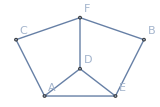

```mathematica
Graph[{
{"A","C",3},
{"A","D",5},
{"A","E",7},
{"D","E",4},
{"C","F",1},
{"D","F",6},
{"F","B",8},
{"E","B",2}}
/.{u_,v_,c_}:>Property[u<->v,EdgeCapacity->c],VertexLabels->"Name"]
```

```mathematica
op=FindMaximumFlow[
{{"A","C",3},
{"A","D",5},
{"A","E",7},
{"D","E",4},
{"C","F",1},
{"D","F",6},
{"F","B",8},
{"E","B",2}}
/.{u_,v_,c_}:>Property[u<->v,EdgeCapacity->c],"A","B","OptimumFlowData"]
```

OptimumFlowData[<6>, <11>]

```mathematica
Grid[{#,op[#]}&/@op["EdgeList"],Frame-> All,Alignment-> Left]
```

A<->C | 3
A<->D | 5
A<->E | 7
C<->A | 2
C<->F | 1
D<->A | 3
D<->F | 6
E<->A | 1
E<->D | 4
E<->B | 2
F<->B | 7

```mathematica
PropertyValue[{op["FlowGraph"],"B"<->"F"},EdgeCapacity]
```

8

```mathematica
Clear[maxFlowGraph]
maxFlowGraph[opf_OptimumFlowData]:=
Graph[
ReplaceAll[
Normal@GroupBy[
opf["EdgeList"],
Sort->(e↦(2Boole@OrderedQ[e]-1)opf[e]),
Total],
{(u_<->v_->c_):>If[Positive[c],Labeled[u->v,c],Labeled[v->u,-c]]}],
VertexLabels->"Name"]
```

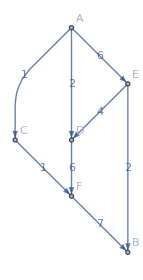

```mathematica
maxFlowGraph[op]
```

```mathematica
Subtract[x]
```

Subtract::argr: Subtract called with 1 argument; 2 arguments are expected.

Subtract[x]

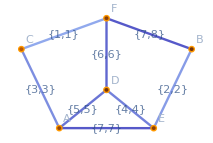

```mathematica
Graph[op["FlowGraph"],VertexLabels->"Name",EdgeLabels->((#->{op[#],PropertyValue[{op["FlowGraph"],#},EdgeCapacity]})&/@op["EdgeList"])]
```

```mathematica
FindMaximumFlow[]
```

```mathematica
NestWhile[NextKSubset[Range[Binomial[n+1,2]-1],#]&,Range[n-1],test]
```

```mathematica
NextKSubset[{1,2,3,4},{1,2}]
```

{1,3}

```mathematica
Clear[baseLine]
baseLine[n_Integer]:=NestList[NextKSubset[Range[Binomial[n+1,2]-1],#]&,Range[n-1],5]
```

```mathematica
baseLine[3]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4}}

```mathematica
Binomial[(n+1) n/2,n]n!/(Binomial[(n+1) n/2-1,n-1] n!)//FullSimplify
```

(1+n)/2

```mathematica
(DuplicateFreeQ@*Abs@*Differences)[{1,2,4,5,3,7,4}]
```

False

```mathematica
(Abs@*Differences)[{1,2,4,5,3,7,4}]
```

```mathematica
Equal[{1,2,1,2,4,3}]
```

True

```mathematica
Compile
```

```mathematica
Column@NestList[Abs@*Differences,#,Length[#]-1]&/@baseLine/@Range[5]
```

{{1},{1,3}
{2},{1,6,4}
{5,2}
{3},{6,1,10,8}
{5,9,2}
{4,7}
{3},{6,14,15,3,13}
{8,1,12,10}
{7,11,2}
{4,9}
{5}}

```mathematica
Differences[{1,2,3}]
```

{1,1}

```mathematica
solveTriangle[2]
```

{{Abs[x[2,1]-x[2,2]]==x[1,1],0<x[1,1]<3,0<x[2,1]<3,0<x[2,2]<3,x[1,1]≠x[2,1],x[1,1]≠x[2,2],x[2,1]≠x[2,2]},{x[1,1],x[2,1],x[2,2]},Integers}

```mathematica
solveTriangle2[n_Integer]:=Module[{vars=Flatten@Table[x[i,j],{i,n},{j,i}]},
Permutations]]
```

```mathematica
1/89.
```

0.011236

```mathematica
Query[
"核算办法",
Select[#产生方式=="模板"&],
f]@核算设计//InputForm
```

{f[<|"业务名称" -> "Tn证券买入", "存储过程" -> "sp_Cust_PT_Tnbuy", 
   "业务摘要" -> "220100", "流通类型" -> "0", "核算类型" -> "证券买入", 
   "动作类型" -> "0B", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "沪港通股票买入", "存储过程" -> "sp_Cust_HG_Gpmr", 
   "业务摘要" -> "220094", "流通类型" -> "0", "核算类型" -> "证券买入", 
   "动作类型" -> "0B", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "报价融券回购", "存储过程" -> "sp_Cust_BJHG_Rq", 
   "业务摘要" -> "220006", "流通类型" -> "7", "核算类型" -> "证券买入", 
   "动作类型" -> "RR", "产生方式" -> "模板", 
   "说明" -> "以面值从CSC买入债券"|>], 
 f[<|"业务名称" -> "融资买入", "存储过程" -> "sp_Cust_RZRQ_Rzmr", 
   "业务摘要" -> "550002", "流通类型" -> "0", "核算类型" -> "证券买入", 
   "动作类型" -> "0B", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "查询收费", "存储过程" -> "sp_Cust_PT_Cxsf", 
   "业务摘要" -> "222006", "流通类型" -> "-", "核算类型" -> "其它费用", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "沪港通组合费", "存储过程" -> "sp_Cust_HG_Zhf", 
   "业务摘要" -> "220097", "流通类型" -> "-", "核算类型" -> "其它费用", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> "由香港结算收取"|>], 
 f[<|"业务名称" -> "股息红利差异扣税", "存储过程" -> "sp_Cust_PT_Hltax", 
   "业务摘要" -> "140203", "流通类型" -> "-", "核算类型" -> "利息扣税", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "股息红利扣税蓝补", "存储过程" -> "sp_Cust_ZJCQ_Gxhlkslb", 
   "业务摘要" -> "140205", "流通类型" -> "-", "核算类型" -> "利息扣税", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "指定交易", "存储过程" -> "sp_Cust_PT_Zdjy", 
   "业务摘要" -> "220032", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "撤销指定", "存储过程" -> "sp_Cust_PT_Cxzd", 
   "业务摘要" -> "220033", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "港股通指定交易", "存储过程" -> "sp_Cust_HG_Zdjy", 
   "业务摘要" -> "220118", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "港股通撤指交易", "存储过程" -> "sp_Cust_HG_Czjy", 
   "业务摘要" -> "220119", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "台帐间现金划转存", "存储过程" -> "sp_Cust_ZJCQ_Tzxjc", 
   "业务摘要" -> "140055", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "台帐间现金划转取", "存储过程" -> "sp_Cust_ZJCQ_Tzxjq", 
   "业务摘要" -> "140057", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "删除过期证券", "存储过程" -> "sp_Cust_PT_Scgqzq", 
   "业务摘要" -> "110434", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "投票确认", "存储过程" -> "sp_Cust_PT_Tpqr", 
   "业务摘要" -> "222004", "流通类型" -> "-", "核算类型" -> "无需核算", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "三方存管现金蓝补", "存储过程" -> "sp_Cust_ZZCQ_Sfcgxjlb", 
   "业务摘要" -> "940008", "流通类型" -> "-", "核算类型" -> "资金调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "三方存管现金红冲", "存储过程" -> "sp_Cust_ZZCQ_Sfcgxjhc", 
   "业务摘要" -> "940029", "流通类型" -> "-", "核算类型" -> "资金调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "现金蓝补", "存储过程" -> "sp_Cust_QZCQ_Xjlb", 
   "业务摘要" -> "140008", "流通类型" -> "-", "核算类型" -> "资金调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "现金红冲", "存储过程" -> "sp_Cust_QZCQ_Xjhc", 
   "业务摘要" -> "140029", "流通类型" -> "-", "核算类型" -> "资金调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "支票蓝补", "存储过程" -> "sp_Cust_QZCQ_Zplb", 
   "业务摘要" -> "140009", "流通类型" -> "-", "核算类型" -> "资金调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "支票红冲", "存储过程" -> "sp_Cust_QZCQ_Zphc", 
   "业务摘要" -> "140030", "流通类型" -> "-", "核算类型" -> "资金调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "证券蓝补", "存储过程" -> "sp_Cust_PT_Zqlb", 
   "业务摘要" -> "150002", "流通类型" -> "-", "核算类型" -> "持仓调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "证券红冲", "存储过程" -> "sp_Cust_PT_Zqhc", 
   "业务摘要" -> "150001", "流通类型" -> "-", "核算类型" -> "持仓调整", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "银行转证券", "存储过程" -> "sp_Cust_CG_Yzzr", 
   "业务摘要" -> "160021", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "存折存", "存储过程" -> "sp_Cust_ZJCQ_Czc", 
   "业务摘要" -> "140002", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "现金存", "存储过程" -> "sp_Cust_ZJCQ_Xjc", 
   "业务摘要" -> "140001", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "银证转帐调帐存", "存储过程" -> "sp_Cust_ZZCQ_Yzzztzc", 
   "业务摘要" -> "160031", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "转帐支票存", "存储过程" -> "sp_Cust_ZJCQ_Zzzpc", 
   "业务摘要" -> "140004", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "OCT资金划入", "存储过程" -> "sp_Cust_ZJCQ_Otcr", 
   "业务摘要" -> "140211", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "调帐转帐转入", "存储过程" -> "sp_Cust_ZZCQ_Tzzzr", 
   "业务摘要" -> "168007", "流通类型" -> "-", "核算类型" -> "资金存入", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "证券转银行", "存储过程" -> "sp_Cust_CG_Yzzc", 
   "业务摘要" -> "160022", "流通类型" -> "-", "核算类型" -> "资金取出", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "存折取", "存储过程" -> "sp_Cust_ZJCQ_Czq", 
   "业务摘要" -> "140022", "流通类型" -> "-", "核算类型" -> "资金取出", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "现金取", "存储过程" -> "sp_Cust_ZJCQ_Xjq", 
   "业务摘要" -> "140021", "流通类型" -> "-", "核算类型" -> "资金取出", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "转帐支票取", "存储过程" -> "sp_Cust_ZJCQ_Zzzpq", 
   "业务摘要" -> "140024", "流通类型" -> "-", "核算类型" -> "资金取出", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "OCT资金划出", "存储过程" -> "sp_Cust_ZJCQ_Otcc", 
   "业务摘要" -> "140212", "流通类型" -> "-", "核算类型" -> "资金取出", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>], 
 f[<|"业务名称" -> "调帐转帐转出", "存储过程" -> "sp_Cust_ZZCQ_Tzzzc", 
   "业务摘要" -> "168008", "流通类型" -> "-", "核算类型" -> "资金取出", 
   "动作类型" -> "-", "产生方式" -> "模板", "说明" -> ""|>]}

```mathematica
AppendTo[核算设计,(* 借方余额 = 1，贷方余额 = -1 *)
"科目信息"->Association@Query["表字段定义",
Select[StringMatchQ[#类型,"表*方"]&],
#变量名称-><|"科目方向"->2Boole@StringMatchQ[#类型,"*借方"]-1,"表"->#表|>&
]@核算设计];
```

```mathematica
AppendTo[核算设计,
"数据字典"->Normal@KeyMap[WordBoundary~~#~~WordBoundary&]@Join[Query["核算输入输出",All,"数据库表"]@核算设计,
Association@Query["表字段定义",All,(#变量名称->Query["核算输入输出",#表,"数据库表"][核算设计]<>"."<>#字段)&]@核算设计]];
```

```mathematica
AppendTo[核算设计,(* 不同业务下各科目的发生额 *)
"业务核算"->Map[KeyDrop["表外对拆"]]@Query[
"会计分录",
(e↦GroupBy[e,
Key["核算类型"]->(
<|#借方->核算设计["科目信息",#借方,"科目方向"]ToExpression[StringReplace[#金额,"."->"$"]],
#贷方->-核算设计["科目信息",#贷方,"科目方向"]ToExpression[StringReplace[#金额,"."->"$"]]|>&),
Merge[Total/*InputForm/*ToString]])
]@核算设计];
```

```mathematica
AppendTo[核算设计,
"会计分录文本"->Query["核算设计文本",
Association@StringCases[
StringExpression[
StartOfLine~~"#+NAME: acc:会计分录"~~Whitespace,
tcnt:Shortest["|-"~~__~~"-|\n"],
"\n"]:>(StringTrim@First@StringSplit[StringSplit[tcnt,"\n"][[4]],"|"]->tcnt)]
]@核算设计];
```

```mathematica
Clear[映射字段, 存储过程]

映射字段[中文字段_List]:=StringRiffle[StringReplace[中文字段,核算设计["数据字典"]],", "]

存储过程[业务类型_String]:=Module[{持仓核算字段,资金核算字段},
{持仓核算字段,资金核算字段}=Map[t↦Query["业务核算",业务类型,KeySelect[核算设计["科目信息",#,"表"]==t&]]@核算设计]@{"持仓核算","资金核算"};
TemplateApply[核算设计["存储过程模板"],
Join[
Query["核算输入输出",All,"数据库表"]@核算设计,
Query["核算办法",业务类型]@核算设计,
<|
"会计分录"->核算设计["会计分录文本",业务类型],
"业务类型" -> 业务类型, 
"流通类型" ->"'"<>StringTake["0"<>核算设计["核算办法",业务类型,"流通类型"],-2]<>"'",
"持仓核算字段"->", "<>映射字段[Keys@持仓核算字段],
"持仓核算发生额"->", "<>映射字段[Values@持仓核算字段],
"资金核算字段"->", "<>映射字段[Keys@资金核算字段],
"资金核算发生额"->", "<>映射字段[Values@资金核算字段],
"持仓核算更新"->映射字段[KeyValueMap[#1<>" = "<>#2&,持仓核算字段]],
"资金核算更新"->映射字段[KeyValueMap[#1<>" = "<>#2&,资金核算字段]]
|>]]]
```

```mathematica
AppendTo[核算设计,
"存储过程模板"->
Import["sp.template","Text",CharacterEncoding->"UTF8"]];
```

```mathematica
Export["test.sql",TemplateApply[Import["tpl_merge.sql","Text",CharacterEncoding->"UTF8"], <|"业务流水表"->"logasset_hs","持仓核算表"->"stkasset_hs", "业务类型" -> "红利入账", "业务摘要" -> "221007","会计分录"->核算设计["会计分录文本","红利入账"]|>],"Text",CharacterEncoding->"UTF8"]
```

```mathematica
Nest[t↦TemplateApply[t,<|"业务流水表"->"logasset_hs","持仓核算表"->"stkasset_hs", "业务类型" -> "红利入账", "业务摘要" -> "221007","会计分录"->核算设计["会计分录文本","红利入账"]|>],Import["tpl_merge.sql","Text",CharacterEncoding->"UTF8"],2]
```

```mathematica
Intersection[Keys@核算设计["业务核算","红利入账"],Query["表字段定义",Select[#表=="资金核算"&&StringMatchQ[#类型,"表*方"]&]/*Keys]@核算设计]
```

{账户资金}

```mathematica
核算设计["业务核算","红利入账"]
```

<|账户资金→成交金额,利息收入→成交金额,表外对拆→成交金额,红利金额→成交金额|>

```mathematica
TemplateApply[核算设计["存储过程模板","会计核算"],
<|"业务流水表"->"logasset_hs",
"持仓核算表"->"stkasset_hs", 
"业务类型" -> "红利入账", 
"业务摘要" -> "221007",
"会计分录"->核算设计["会计分录文本","红利入账"]|>]
```

/***************************************************
    业务类型:	红利入账
    业务摘要:	221007


    本存储过程由以下会计分录自动生成：

|----------+----------+----------+----------+--------------|
| 业务类型 | 借方     | 贷方     | 金额     | 说明         |
|----------+----------+----------+----------+--------------|
| 红利入账 | 账户资金 | 利息收入 | 成交金额 | 利息收入入账 |
|----------+----------+----------+----------+--------------|
| 红利入账 | 表外对拆 | 红利金额 | 成交金额 | 红利金额记录 |
|----------+----------+----------+----------+--------------|


*/

if exists (select * from sysobjects where type = 'P' and name = 'sp_221007')
	drop procedure sp_221007
go

create procedure sp_221007(
	@bizdate int,  
	@msg varchar(128) = null output)
as
begin try
	begin transaction

		-- 更新持仓核算表
	merge into  as sec
	using (
		select serverid, orgid, custid, fundid, market, stkcode,  as ltlx
		from 
		where digestid =  and bizdate = @bizdate
	) as ord
	on (
		sec.serverid = ord.serverid and
		sec.orgid = ord.orgid and
		sec.custid = ord.custid and
		sec.fundid = ord.fundid and
		sec.market = ord.market and
		sec.ltlx = ord.ltlx and
		sec.stkcode = ord.stkcode)
	when matched then
		update set 
	when not matched then
		insert (serverid, orgid, custid, fundid, market, stkcode, ltlx)  
		values (ord.serverid, ord.orgid, ord.custid, ord.fundid, ord.market, ord.stkcode, ord.ltlx);

	

	select @msg='核算处理成功'

	update logasset_hs set sett_status = 3, sett_remark = @msg
	where  bizdate = @bizdate and digestid = 221007 and bizdate = @bizdate

	commit transaction
	return 0
end try

begin catch
	if @@trancount > 0
		rollback transaction
	
	return -1
end catch

go

```mathematica
StringReplace[Keys@First@KeyIntersection[{核算设计["业务核算","红利入账"],
Query["表字段定义",Select[#表=="持仓核算"&]]@核算设计}]]
```

{"利息收入", "红利金额"}

```mathematica
translateDB[biz_String->params_]:=biz->Map[Lookup[科目增减[biz],#,#]&,params]
```

```mathematica
Query["公共过程参数",All,"赋值"]@核算设计
```

<|@action→,@matchqty→成交数量,@matchamt→成交金额,@matchamt_ex→0,@aiamount→0,@fundeffect→账户资金,@stkeffect→库存数量,@stkcost_ch→库存成本,@syvalue_ch→交易收益,@aicost_ch→利息成本,@lxsr_ch→利息收入,@fee→总费用,@jsxf→净手续费,@yhs→印花税,@ghf→过户费,@qtfee→其它费,@lxs→利息税|>